# Universal Estimator

Given the pdf of some distribution and a sample containing m observations drawn from dist using pdf with true parameter θ, The UniversalEstimator(pdf, sample, θ) returns  a 
tuple (Overscript[θ, ^], e, CRB) where Overscript[θ, ^] is the predicted parameter, e is the abs-error | θ - Overscript[θ, ^] | and CRB is the Cramer-Rao-Bound (θ, m) on the error of an unbiased estimator.

## Auxiliary Functions

Auxiliary functions used by the Universal Estimator

## Fisher Information and Cramer-Rao bound

Fisher information for a distribution with a single parameter θ

```mathematica
FisherInformation[dist_]:=Module[{f},
(*let f be the PDF of dist with parameter θ evaluated at x*)
f = PDF[dist[θ],x];
(*method-1*)
Expectation[D[Log[f], {θ}]^2,x\[Distributed]dist[θ]]
(*method-2*)
(*-Expectation[D[Log[f],{θ,2}],x\[Distributed]dist[θ]]*)
]
```

Cramer-Rao bound for a single parameter d and m observations

```mathematica
CRB[dist_, d_, m_]:=(
fi=FisherInformation[dist];
FI[θ_]:=Evaluate[fi];
(1/FI[d])/m
)
```

#### Examples

#### Poisson distribution

Poisson distribution with mean λ

```mathematica
FisherInformation@PoissonDistribution
```

1/θ

```mathematica
CRB[PoissonDistribution, 3, 256]
```

3/256

#### Normal distribution

```mathematica
NormalDistribution1D[σ_]:=NormalDistribution[0,σ];
```

```mathematica
FisherInformation@NormalDistribution1D
```

2/θ^2

```mathematica
CRB[NormalDistribution1D, 3, 256]
```

9/512

#### LogNormal distribution

LogNormal distribution with a mean μ  and a standard deviation σ (fix μ = 0)

```mathematica
LogNormalDistribution1D[σ_]:=LogNormalDistribution[0,σ];
```

```mathematica
FisherInformation@LogNormalDistribution1D
```

2/θ^2

```mathematica
CRB[LogNormalDistribution1D, 3, 256]
```

9/512

#### PowerLaw distribution

PowerLaw distribution with domain parameter k and shape parameter a (fix k = 1)

```mathematica
PowerDistribution1D[a_]:=PowerDistribution[1,a]
```

```mathematica
FisherInformation@PowerDistribution1D
```

1/θ^2

```mathematica
CRB[PowerDistribution1D, 3, 256]
```

9/256

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
```

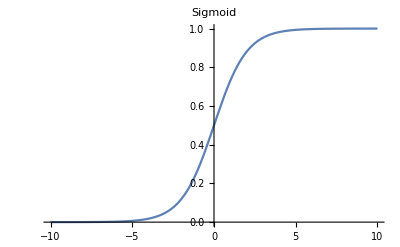

```mathematica
Plot[Sigmoid[x], {x, -10, 10}, PlotLabel->HoldForm[Sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

```mathematica
Logit[x_]:= Log[x/(1-x)]
```

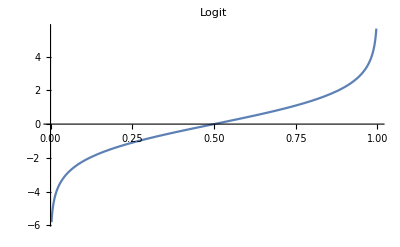

```mathematica
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

We define an Adjuster function which accept the original parameter range (low, high) and returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.
We use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

## Universal Estimator

Given a distribution  dist(x|θ) and the range for the parameter θ,  UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

#### Input

dist: a distribution (e.g: PoissonDistribution)

range: the range R_θ of the parameter θ

#### Processing and output

Define a sample generator g(θ, m) for generating samples from the distribution dist with the parameter θ

g(θ,m) uses a pseudorandom variate for drawing a sample with m observations from the symbolic distribution dist using the parameter θ

Generate learning data {θ_i, H_i} using f(θ, m)

Generate n random parameters t_i ∈ [0, 1]

Adjust t_i ∈ [0, 1] to get corresponding parameters θ_i in the original range

Generate learning samples H_i (each learning sample is a histogram of the sample S_i and the corresponding parameter θ_i)

Train a NN that outputs a model for predicting the parameters θ_i corresponding to the histograms H_i

Return an Estimator(s) function which accepts a sample in its input and returns a prediction for the parameter θ used to generate sample

## Generate Data

Generates synthetic data for learning

Arguments:

n: number of samples to generate

m: number of observations in each sample

f: the (dist) function for generating samples. f(θ, m) returns m observations using parameter θ

range: original range of the dist parameter θ (e.g. [0, ∞])

bins: number of bins in the histograms generated from samples (default: max[samples]+1)

Returns:

a table of associations (one row per sample): histogram -> θ

```mathematica
GenerateData[n_, m_, f_, range_, bins_:-1]:= 
Module[{adjuster, params,samples, nbins, MAXBINS},

(*generate an adjuster for the parameter range*)
adjuster=Adjuster[range[[1]],range[[2]]];

(*generate N random parameters in the range [0,1] and adjust them to the original range*)
params=Table[adjuster[RandomReal[{0,1}]],{i,1,n}];

(*generate N samples from the generated parameters*)
samples=Table[f[params[[i]],m],{i,1,n}];

(*create a histogram for each sample*)
MAXBINS=1000;
nbins=If [bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1]];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];

(*output: a table of associations: histogram -> param over all samples*)
Table[h@samples[[i]]-> params[[i]], {i, 1, n}]
]
```

Example usage

```mathematica
f[α_, m_]:=RandomVariate[WaringYuleDistribution[α],m];
Print[GenerateData[5,10,f, {2,3}]//TableForm];
```

{8,2,0,0,0}→2.75058
{5,3,0,0,2}→2.29066
{8,0,1,1,0}→2.54304
{8,2,0,0,0}→2.36704
{9,1,0,0,0}→2.71041

## DNN

Generate a NN for predicting the parameter θ from an input histogram
The NN is fully connected, the input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
DropoutLayer[0.1],

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
DropoutLayer[0.1],

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 
DropoutLayer[0.1],

LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

#### The UniversalEstimator

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_]:=Module[{g, n, m, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,m_] := RandomVariate[dist[θ],m];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
n =2000; (*number of learning samples*)
m = 256;   (*number of observations in each sample*)
trainSet=GenerateData[n,m,g, range];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[n/4,m,g, range, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>,
Method->"ADAM" ,
BatchSize->256
(*LearningRate->0.001*)
(*LossFunction->MeanAbsoluteLossLayer[]*)
];

Print[trained];

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiments

We use the UniversalEstimator as follows:

Given a distribution dist(x|θ)  and a range R_θ for the values of θ (e.g: [0,∞])

Use UniversalEstimator to generate an  Estimator for dist(x|θ)

Let g be a function for generating samples from dist(x|θ)

g(θ,m) uses a pseudorandom variate for drawing a sample with m observations from the symbolic distribution dist using a parameter θ

Generate parameter test points on the unit range t_i∈ [0, 1] (e.g: {0.1, 0.2, ..., 0.9})

Adjust t_i ∈ [0, 1] to θ_i∈R_θ using the Adjuster function

Generate test samples S_i using θ_i

Use Estimator for predicting the parameters (θ̂)_i

Evaluate the prediction errors e_i=|θ_i - OverHat[θ_i]|

Compute  Cramer-Rao bound at θ_i (hopefully, the prediction errors are near the corresponding Cramer-Rao bounds)

```mathematica
RunExperiment[dist_, range_]:= Module[{estimator, g, adjuster, params, m, samples, Θ, Θhat, e, crb},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range];

(*Create test parameters on the unit range [0,1] and adjust them to the original range*)
adjuster=Adjuster[range[[1]],range[[2]]];
Θ = Table[adjuster[i],{i,0.1,0.9,0.1 }];

(*create test samples*)
m = 256;
g[θ_,m_] := RandomVariate[dist[θ],m];
samples = Table[g[Θ[[i]], m], {i,1,9,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,9,1 }];

(*evaluate prediction errors*)
e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,9,1 }];

(*Compute Cramer-Rao bound at Subscript[θ, i]*)
crb = Table[CRB[dist, Θ[[i]], m], {i,1,Length[Θ]}];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["crb(θ,m): ", crb];
Print["abs(θ-θ̂)/crb(θ,m): ", e/crb];

(*return prediction errors and crb*)
{Θ, e, crb}
]
```

Run the experiment for the PoissonDistribution

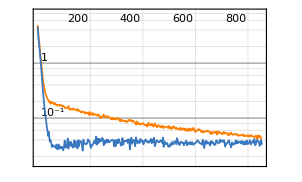
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:6824  rounds:853  time:7.8s  examples/s:223350
data | ,,  training examples:2000  validation examples:500  processed examples:1746944  skipped examples:0
method | ,,  ADAMoptimizer  batch size256CPU
round | ,,  loss:4.01×10^-2
validation | ,,  loss:3.45×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {1.14146,1.29408,1.46127,1.64797,1.8618,2.11545,2.43268,2.8667,3.58702}

θ̂: {1.12352,1.22827,1.30639,1.69736,1.96274,2.23346,2.47618,2.76859,3.23259}

abs(θ-θ̂): {0.0179438,0.0658138,0.15488,0.0493879,0.100942,0.118009,0.0435019,0.0981028,0.354439}

crb(θ,m): {0.00445884,0.00505502,0.0057081,0.0064374,0.00727266,0.00826349,0.00950267,0.011198,0.0140118}

abs(θ-θ̂)/crb(θ,m): {4.02431,13.0195,27.1334,7.67203,13.8797,14.2808,4.57786,8.76071,25.2957}

```mathematica
{Θ, e, crb} = RunExperiment[PoissonDistribution, {1,10}];
```

### Run the experiment for the LogNormalDistribution1D

```mathematica
(*{Θ, e, crb} = RunExperiment[LogNormalDistribution1D, {1,10}];*)
```

#### Run the experiment for the PowerDistribution1D

```mathematica
(*{Θ, e, crb} = RunExperiment[PowerDistribution1D, {2,3}];*)
```